```mathematica
Clear[j,h]
H={{j-2h,0,0,0,0,0,0,0,0},{0,-h,0,j,0,0,0,0,0},{0,0,-j,0,j,0,0,0,0},{0,j,0,-h,0,0,0,0,0},{0,0,j,0,0,0,j,0,0},{0,0,0,0,0,h,0,j,0},{0,0,0,0,j,0,-j,0,0},{0,0,0,0,0,j,0,h,0},{0,0,0,0,0,0,0,0,j+2h}}
```

{{-2 h+j,0,0,0,0,0,0,0,0},{0,-h,0,j,0,0,0,0,0},{0,0,-j,0,j,0,0,0,0},{0,j,0,-h,0,0,0,0,0},{0,0,j,0,0,0,j,0,0},{0,0,0,0,0,h,0,j,0},{0,0,0,0,j,0,-j,0,0},{0,0,0,0,0,j,0,h,0},{0,0,0,0,0,0,0,0,2 h+j}}

```mathematica
e=Eigenvalues[H]
v=Eigenvectors[H]
```

{-h-j,h-j,-2 j,-j,j,-2 h+j,-h+j,h+j,2 h+j}

{{0,-1,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,1,0},{0,0,1,0,-1,0,1,0,0},{0,0,-1,0,0,0,1,0,0},{0,0,1,0,2,0,1,0,0},{1,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1}}

1

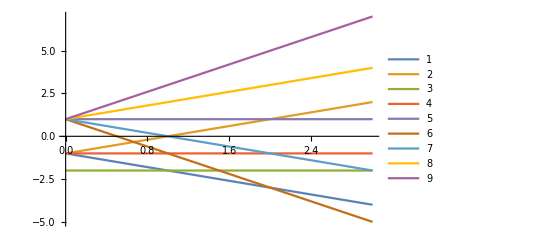

```mathematica
j=1
Plot[e, {h,0,3}, PlotLegends->Automatic]
```